## Setup

```mathematica
(*Set as ...PathtoGithubFolder/DataFiles *)
dire="~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/WadWan21";
SetDirectory[dire];
Get[dire<>"/../init.m"]
```

```mathematica
(*Leo T data from Faerman et al. 2013 model*)
data=Import["~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/LeoT_profiles_Faerman13.dat"];
(*Columns are: r (kpc) n_DM (cm^-3) n_H (cm^-3) n_e (cm^-3) n_HI (cm^-3)*)
data=DeleteDuplicatesBy[data,First];
rl= data[[All,1]];
dml=Interpolation[Transpose[{data[[All,1]],mp/mgev data[[All,2]]}]];
nhl=Interpolation[Transpose[{data[[All,1]],data[[All,3]]}]];
nel=Interpolation[Transpose[{data[[All,1]],data[[All,4]]}]];
nh1l=Interpolation[Transpose[{data[[All,1]],data[[All,5]]}]];
```

InterpolatingFunction::dmval: Input value {0.0000143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

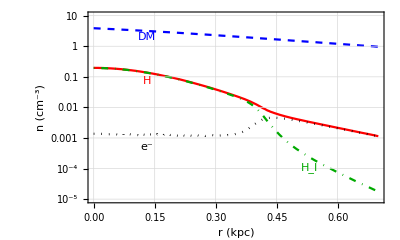

```mathematica
Show[LogPlot[{dml[r],nhl[r],nel[r],nh1l[r]},{r,0,0.7},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.6,FrameLabel->{"r (kpc)","n (cm^-3)"},PlotRange->{{0,0.7},{10^-5,10}},PlotStyle->{{Blue,Dashed},{Red},{Black,Dotted},{Darker[Green],DotDashed},{RGBColor[0.363898, 0.618501, 0.782349],Dashed},{RGBColor[0.647624, 0.37816, 0.614037],DotDashed}}(*PlotRange->{{0.002,10},{4 10^-25,10^-20}},*)],Graphics[{Text[Style["DM",Blue],Scaled[{0.2,0.87}],{0,0},Automatic,{1,0}],Text[Style["H",Red],Scaled[{0.2,0.64}],{0,0},Automatic,{1,0}],Text[Style["e^-",Black],Scaled[{0.2,0.295}],{0,0},Automatic,{1,0}],Text[Style["H_I",Darker[Green]],Scaled[{0.75,0.185}],{0,0},Automatic,{1,0}]}]]
```

```mathematica
coolTot=NIntegrate[4 Pi r^2 7 10^-30,{r,0,0.35}]624;(*Vol integrated cooling rate (GeV kpc^3/cm^3/s), Taken from Kim 21*)
```

```mathematica
(*Thermalization factor, Eq. 3*)
xe=0.012;
fHeat[m_]:=Piecewise[{{1-(1-xe^0.27)^1.32+4 xe^0.4(1-xe^0.34)^2(11/m)^0.7,m>=11},{1-0.213Exp[2(m-11)],m<11}}]
```

#### Parameters for MW clouds

```mathematica
(*DM density of Milky Way NFW halo. Input: r(kpc), output: GeV/cm^3*)
rho0 = 0.89/(4Pi 16 NIntegrate[r/(1+r/16.)^2,{r,0,296}]);
rhoNFW[r_]:=rho0 16/ r/(1+ r/16)^2 (10^12 msun)/(mgev kpc^3)
```

```mathematica
(*Halo conc. mass relation from Maccio et al. 2008*)
cvir[mvir_]:= 10^(1.051-0.099 (mvir-12))
```

```mathematica
(*Scale radius of NFW halo, in kpc*)
rsNFW[m_]:=1/cvir[m]((6.67 10^-8 1.989 10^(33+m))/(100 (70 10^(5-3))^2)1/(3.086 10^21))^(1/3)
```

```mathematica
(*Radial velocity dispersion of DM in km/s in the NFW halo input: [mpc, Log10[mHalo(Msun)]], using Hoeft et al. 14 *)
sigmaDM[r_,m_]:=Sqrt[0.29(1.989 10^(33+m))/(Log[1+cvir[m]]-cvir[m]/(1+cvir[m]))6.67 10^-8 Log[1+r/rsNFW[m]]/(r 3.086 10^21)(1-rsNFW[m]/r Log[1+r/rsNFW[m]])^0.41 1/10^(5 2)]
```

```mathematica
rc=Sqrt[4.68^2+1^2]; tc=400;nc=0.4; vdmc=220; vrelDMc=Sqrt[vdmc^2+3 sigmaDM[rc,12]^2];(*G33.4−8.0 cloud parameters*)
```

```mathematica
(*Cooling Function*)
data=Import["~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/CoolingFunc_Grackle.dat"];
coolFunc=Interpolation[Transpose[{data[[All,1]],data[[All,2]]}]];
```

## DM to photons

We will deal with various scenarios for DM producing photons in this section

### Photon cross-section module

```mathematica
mloglist=Table[i,{i,Log10[27.21],4,0.01}]; 
mloglist2=Table[i,{i,Log10[13.61],6,0.05}];
```

Compiling the photon cross section below by combining limits from different sources

```mathematica
(*For energy<30 eV, we use Band et al. 1990*)
sigH[e_]:= 6.06 10^-16  ((2e)/13.6)^(-3/2) (1+Sqrt[(2e)/13.6])^-4
sigHe[e_]:= 3.94 10^-18  (e/112.88)^(-3/2) (1+Sqrt[e/112.88])^-4
```

```mathematica
(*For photon energy between 30 eV-10keV, we use interaction length data from https://henke.lbl.gov/optical_constants/atten2.html
and for >10keV we use https://physics.nist.gov/PhysRefData/XrayMassCoef/tab3.html*)
dataH=Import["sigma_H_photon.dat"];
dataHe=Import["sigma_He_photon.dat"];
dataH[[All,2]]=mp/(dataH[[All,2]] 10^-4)+4 mp 0.08/(dataHe[[All,2]] 10^-4);(*H+He, calculating effective cross section in cm^2*)
```

```mathematica
data={{0,0},{13.5,0}};
data=Join[data,Table[{e,sigH[e]},{e,13.6,24.5,0.3}],Table[{e,sigH[e]+0.08 sigHe[e]},{e,24.6,29.9,0.3}],dataH];
sigEff=Interpolation[data]; (*Final effective photon cross section*)
```

```mathematica
nhAvg=NIntegrate[nh1l[r],{r,0,0.35},Method->"Trapezoidal"]/0.35; (*Average 1D HI density*)
```

```mathematica
opacity[m_]:=1-Exp[-nhAvg 0.35 kpc sigEff[10^m]]
```

General::munfl: Exp[-783.446] is too small to represent as a normalized machine number; precision may be lost.

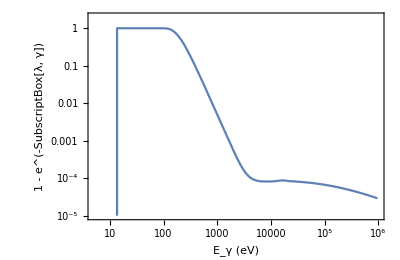

```mathematica
ListLogLogPlot[{Join[{{10^mloglist2[[1]],10^-10}},Table[{10^mloglist2[[i]],opacity[mloglist2[[i]]]},{i,Length[mloglist2]}]]},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400,AspectRatio->0.65,FrameLabel->{Style["E_γ (eV)",18],Style["1 - e^(-SubscriptBox[λ, γ])",20]},PlotRange->{{5,10^6},{10^-5,2}}]
```

### ALP constraints

```mathematica
(*Volume integrated heating within Leo T*)
heat[m_]:=NIntegrate[4 Pi r^2 dml[r]((10^m 10^-9)^3)/(64 Pi) 1.52 10^24 (*s^-1*) ,{r,0,0.35},Method->"Trapezoidal"](1-Exp[-nhAvg 0.35 kpc sigEff[10^m/2]])fHeat[10^m/2-13.6](1-2 13.6/10^m)
```

```mathematica
plot=Table[{10^mloglist[[i]],Sqrt[coolTot/heat[mloglist[[i]]]]},{i,Length[mloglist]}];
plot=Join[{{27.2,1}},plot];
```

General::munfl: Exp[-761.742] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
(*Milky way gas cloud heating*)
heat[m_]:=((10^m 10^-9)^3)/(64 Pi) rhoNFW[rc]1.52 10^24 (*s^-1*) fHeat[10^m/2-13.6](1-2 13.6/10^m)(1-Exp[-nc 13.9 pc sigEff[10^m/2]])
```

```mathematica
(*Bounds from MW gas clouds*)
plot2=Table[{10^mloglist[[i]],Sqrt[nc^2 coolFunc[tc] 624/heat[mloglist[[i]]]]},{i,Length[mloglist]}];
plot2=Join[{{27.2,1}},plot2];
```

```mathematica
(*Producing dashing shown in plots*)
epInt=Interpolation[Transpose[{Log10[plot[[;;,1]]],Log[plot[[;;,2]]]}]];
dashing=Table[{{10.^i,Exp[epInt[i]]},{10.^(i+1),Exp[epInt[i]] 10^10}},{i,1.7,5,0.3}];
dashing=Join[{{{10.^1.45,10^-12},{10.^(1.45+1),10^-2}}},dashing];
```

InterpolatingFunction::dmval: Input value {4.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Data for other bounds*)
data2={{0.00001182137822475099,1.648533826 10^-16},{0.00001182137822475099 10^10,1.648533826 10^-6}};
data3={{0.01052329872108498, 2.627393166064287 10^-11},{1083.453125076008, 0.0000026434042772659304}};
data4=Import["Axions/BolChl21.dat"];
data5=Import["Axions/Reg21.dat"];
data6=Import["Axions/Gri07.dat"];
data7=Import["Axions/XMM.dat"];
data8=Import["Axions/EBL.dat"];
data9=Import["Axions/x_ion.dat"];
data10=Import["Axions/HorizontalBranch.dat"][[3;;]];
```

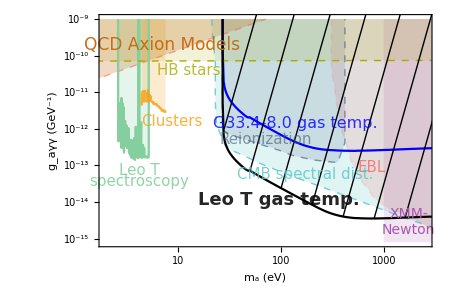

```mathematica
Show[ListLogLogPlot[{plot2,data2,data3,data4,data5,data6,data7,data8,data9,data10,plot},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,(*PlotLabel->Style["Decay: χ → γγ",19,Black],*)Filling->{2->{{3},{RGBColor[0.772079, 0.431554, 0.102387, 0.25]}},4->{Top,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]},5->{Top,RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.2]},6->{Top,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.2]},7->{Top,RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.15]},8->{Top,RGBColor[1, Rational[1, 3], Rational[1, 3], 0.14]},9->{Top,RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667, 0.15]},10->{Top,RGBColor[Rational[2, 3], Rational[2, 3], 0, 0.15]}},FillingStyle->{Opacity[0.3]},FrameLabel->{Style["m_a (eV)",18],Style["g_aγγ  (GeV^-1)",18]},PlotStyle->{Blue,{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],Dashed,Thin},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],Dashed,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashed,Thin},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331]},RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],Dashed,Thin},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.14],Dashed,Thin},{RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667, 0.6],Dashed,Thin},{RGBColor[Rational[2, 3], Rational[2, 3], 0],Dashed,Thin},Black},PlotRange->{{2,2500},{10^-15.1,10^-9}}],Graphics[{Text[Style["QCD Axion Models",RGBColor[0.772079, 0.431554, 0.102387],17],Scaled[{0.19,0.87}],{0,0},{2,0.6}],
Text[Style["Leo T",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.9],15],Scaled[{0.12,0.33}],{0,0},{2,0}],
Text[Style["spectroscopy",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.9],15],Scaled[{0.12,0.28}],{0,0},{2,0}],
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.54,0.20}],{0,0},Automatic,{1,-0.45}],
Text[Style["Clusters",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.22,0.54}],{0,0},{2,0}],
Text[Style["HB stars",RGBColor[Rational[2, 3], Rational[2, 3], 0, 0.8],15],Scaled[{0.27,0.76}],{0,0},{2,0}],
Text[Style["XMM-",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],14],Scaled[{0.93,0.14}],{0,0},{2,0}],
Text[Style["Newton",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],14],Scaled[{0.93,0.07}],{0,0},{2,0}],
Text[Style["EBL",RGBColor[1, Rational[1, 3], Rational[1, 3], 0.7000000000000001],15],Scaled[{0.82,0.34}],{0,0},{1,0}],
Text[Style["CMB spectral dist.",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],15],Scaled[{0.62,0.31}],{0,0},{1,-0.3}],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],16],Scaled[{0.59,0.53}],{0,0},Automatic,{1,-0.33}],
Text[Style["Reionization",RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667, 0.6],15],Scaled[{0.5,0.46}],{0,0},{1,-0.27}]}],ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin}}]]
```

We will now translate these constraints for other DM models below

### DM -> γγ (Decay)

```mathematica
tauLeoT[mS_]:=NIntegrate[4 Pi r^2 dml[r] ,{r,0.,0.35},Method->"Trapezoidal"](1-Exp[-0.1085 0.35 kpc sigEff[mS/2]])fHeat[mS/2-13.6]*(1-2 13.6/mS);
```

```mathematica
tauMW[mS_]:=rhoNFW[rc]fHeat[mS/2-13.6]*(1-2 13.6/mS)(1-Exp[-nc 13.9 (kpc/1000) sigEff[mS/2]]);
```

General::munfl: Exp[-969.45] is too small to represent as a normalized machine number; precision may be lost.

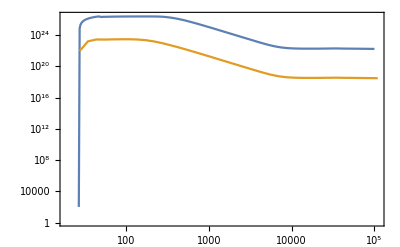

```mathematica
LeoTdata=Join[{{26.915,100}},Table[{10^mS,tauLeoT[10^mS]/coolTot},{mS,1.44,5,0.01}]];
MWdata=Table[{10^mS,tauMW[10^mS]/(nc^2 coolFunc[tc] 624)},{mS,1.44,5.1,0.1}];
ListLogLogPlot[{LeoTdata,MWdata}]
(*Export[dir<>"/photonDecay/LeoTdata.dat",LeoTdata,"Data"];*)
(*Export[dir<>"/photonDecay/MWdata.dat",MWdata,"Data"];*)
```

### CP even scalar

```mathematica
heatS[mS_]:=NIntegrate[4 Pi r^2 dml[r] 1.13 10^-6 (mS/1000)^3 ,{r,0.,0.35},Method->"Trapezoidal"](1-Exp[-0.1 0.35 kpc sigEff[mS/2]])*fHeat[mS/2];
```

```mathematica
scalarLeoT=Table[{LeoTdata[[i,1]],Sqrt[1/LeoTdata[[i,2]]/(1.13 10^-6 (LeoTdata[[i,1]]/1000)^3)]},{i,1,358}];

scalarMW=Table[{MWdata[[i,1]],Sqrt[1/MWdata[[i,2]]/(1.13 10^-6 (MWdata[[i,1]]/1000)^3)]},{i,1,37}];
```

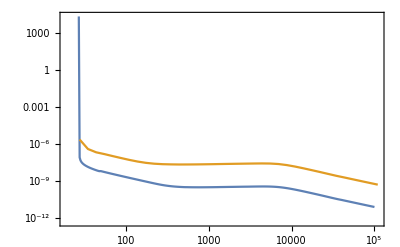

```mathematica
ListLogLogPlot[{scalarLeoT,scalarMW}]
```

```mathematica
(*Export[dir<>"/scalar/scalarLeoT.dat",scalarLeoT,"Data"];
Export[dir<>"/scalar/scalarMW.dat",scalarMW,"Data"];*)
```

### sterile ν

```mathematica
nuLeoT=Table[{LeoTdata[[i,1]],1/(0.5LeoTdata[[i,2]])/(5.5 10^-22(LeoTdata[[i,1]]/1000)^5)},{i,1,358}];

nuMW=Table[{MWdata[[i,1]],1/(0.5MWdata[[i,2]])/(5.5 10^-22(MWdata[[i,1]]/1000)^5)},{i,1,37}];
```

```mathematica
(*Export[dir<>"/nu/nuLeoT.dat",nuLeoT,"Data"];
Export[dir<>"/nu/nuMW.dat",nuMW,"Data"];*)
```

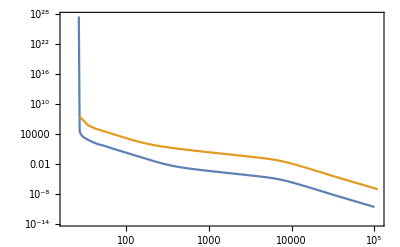

```mathematica
ListLogLogPlot[{nuLeoT,nuMW}]
```

### χχ→γγ (Annihilation)

```mathematica
sWave[m_]:=NIntegrate[4 Pi r^2 dml[r]^2/(10^-9 m) ,{r,0.,0.35},Method->"Trapezoidal"](1-Exp[-0.1085 0.35 kpc sigEff[m]])fHeat[m-13.6]*(1-13.6/m);
```

```mathematica
LeoTswave = Join[{{13.6,1. 10^-26}},Table[{10^m,coolTot/sWave[10^m]},{m,Log10[13.6],5,0.01}]];
```

General::munfl: Exp[-739.126] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
MWswave=Table[{10^m,nc^2 coolFunc[tc] 624/(rhoNFW[rc]/(10^(m-9))fHeat[10^m-13.6]*(1-13.6/10^m)*(1-Exp[-nc 13.9 (kpc/1000) sigEff[10^m]]))},{m,Log10[13.6],5,0.01}];
```

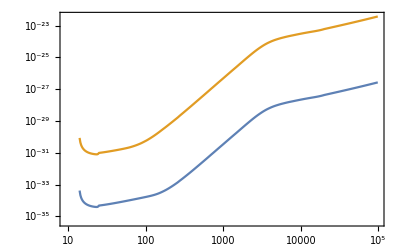

```mathematica
ListLogLogPlot[{LeoTswave,MWswave},Joined->True]
```

```mathematica
(*Export[dir<>"/MWswave.dat",MWswave,"Data"];
Export[dir<>"/LeoTswave.dat",LeoTswave,"Data"];*)
```

## DM to e^+e^-

We will deal with various scenarios for DM producing photons in this section

Let us first calculate some of the numerical values quoted in the paper

```mathematica
0.0005/(0.30286  1.95 10^-20 5.06 10^13 10^-6) /pc(*gyration radius*)
```

5.42184×10^-10

```mathematica
2.18/Sqrt[0.0012] (*Ion Alfven velocity Wikipedia*)
```

62.9312

```mathematica
2.18 /Sqrt[0.06*1.32]  (*Neutral Alfven velocity*)
```

7.74629

```mathematica
350 pc/(63 10^5)/(10^6 year) 3.5 (*Lifetime*)
```

19.0252

```mathematica
mloglist=Table[i,{i,6.005,9.5,0.03}];
```

```mathematica
(*Stopping power of H, He taken from https://www.nist.gov/pml/stopping-power-range-tables-electrons-protons-and-helium-ions
and then scaled by masses and relative fraction*)
dataH=Import["StopPow_H.dat"][[9;;]];
dataHe=Import["StopPow_He.dat"][[9;;]];
dataH[[All,2]]=dataH[[All,2]]mp+4 mp 0.08dataHe[[All,2]];
StopPow=Interpolation[dataH];
```

```mathematica
opacity[m_]:=1-Exp[-0.06(cv 19 10^6 year) StopPow[10^(m-6)]/(10^(m-6))]
```

```mathematica
ticks={{10^6,"10^6",{0.01,0}},{10^7,"10^7",{0.01,0}},{10^8,"10^8",{0.01,0}},{10^9,"10^9",{0.01,0}}};
```

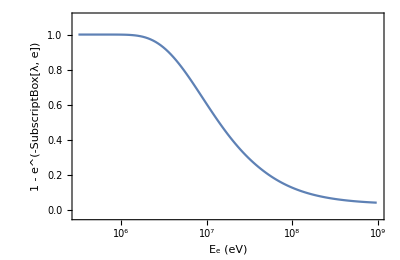

```mathematica
ListLogLinearPlot[{Table[{10^(mloglist[[i]]-0.5),opacity[mloglist[[i]]-0.5]},{i,Length[mloglist]}]},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400,AspectRatio->0.65,FrameTicks->{ {Automatic,Automatic},{ticks,Automatic}},FrameLabel->{Style["E_e (eV)",18],Style["1 - e^(-SubscriptBox[λ, e])",20]},PlotRange->{{10^5.5,10^9},{-0.03,1.1}}]
```

### DM decay lifetime bound

```mathematica
(*Volume integrated heating within Leo T*)
heat[m_]:=NIntegrate[4 Pi r^2 dml[r] ,{r,0,0.35}] fHeat[(10^m- 10^6)/2](10^m- 10^6)/10^m(1-Exp[-0.06(cv 19 10^6 year) StopPow[(10^(m-6)- 1)/2]/((10^(m-6)- 1)/2)])
```

```mathematica
plot=Table[{10^mloglist[[i]],heat[mloglist[[i]]]/coolTot},{i,Length[mloglist]}];
```

General::munfl: Exp[-26458.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-799.321] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {1008.68} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1080.86} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1158.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Milky way gas cloud heating*)
heat[m_]:=rhoNFW[rc] fHeat[(10^m- 10^6)/2](10^m- 10^6)/10^m (1-Exp[-nc(cv (13.9 pc)^2/(6 3 10^27 (10^(m-9)/2- .5 10^-3)^(1/2))) StopPow[(10^(m-6)- 1)/2]/((10^(m-6)- 1)/2)])
```

```mathematica
plot2=Table[{10^mloglist[[i]],heat[mloglist[[i]]]/(nc^2 coolFunc[tc] 624)},{i,Length[mloglist]}];
```

General::munfl: Exp[-12504.8] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {1008.68} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1080.86} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1158.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Producing dashing shown in plots*)
epInt=Interpolation[Transpose[{Log10[plot[[All,1]]],Log[plot[[All,2]]]}]];
dashing=Table[{{10.^(i-1),Exp[epInt[i]] 10^-5},{10.^i,Exp[epInt[i]]}},{i,6.5,11,0.8}];
```

InterpolatingFunction::dmval: Input value {9.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Data for other bounds*)
data2=Import["ElectronDecay/CMB.dat"];
data3=Import["ElectronDecay/IGM.dat"];
data4=Import["ElectronDecay/Essig.dat"];
data5=Import["ElectronDecay/Voyager.dat"];
```

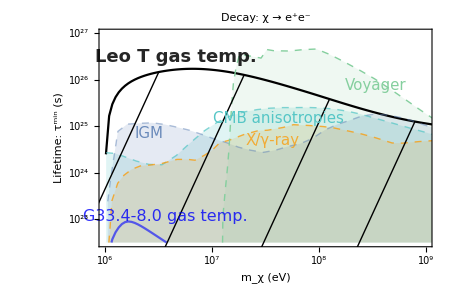

```mathematica
Show[ListLogLogPlot[{plot,plot2,data2,data3,data4,data5},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,FrameTicks->{ {"",},{ticks,}},FillingStyle->{Opacity[0.3]}, PlotLabel->Style["Decay: χ → e^+e^-",19,Black],FrameLabel->{Style["m_χ (eV)",18],Style["Lifetime: τ^min (s)",18]},Filling->{3->{Bottom,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]},4->{Bottom,RGBColor[0.368417, 0.506779, 0.709798, 0.16]},5->{Bottom,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.15]},6->{Bottom,RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.13]}},PlotStyle->{Black,RGBColor[0, 0, 1, 0.6],{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.72],Dashed,Thin},{RGBColor[0.368417, 0.506779, 0.709798, 0.49],Dashed,Thin},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed,Thin},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed,Thin}},PlotRange->{{10^6,10^9},{10^22.5,10^27.}}],
Graphics[{Text[Style["Voyager",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],15],Scaled[{0.83,0.74}],{0,0},{1,-0.5}],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],16],Scaled[{0.2,0.14}],{0,0},Automatic,{1,0.}],
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.23,0.87}],{0,0},Automatic,{1,0.}],
Text[Style["X/γ-ray",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.52,0.49}],{0,0},{1,0.15}],Text[Style["CMB anisotropies",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]],15],Scaled[{0.54,0.59}],{0,0},{1,0.1}],
Text[Style["IGM",RGBColor[0.368417, 0.506779, 0.709798, 0.91],15],Scaled[{0.15,0.52}],{0,0},{1,0}]}],ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin}}]]
```

### DM annihilation bounds

```mathematica
data2=Import["ElectronAnnhilation/Planck.dat"];
data3=Import["ElectronAnnhilation/Integral.dat"];
data4=Import["ElectronAnnhilation/Voyager.dat"];
data5=Import["ElectronAnnhilation/Essig.dat"];
data6=Import["ElectronAnnhilation/Planck_p-wave.dat"];
data7=Import["ElectronAnnhilation/Fermi.dat"];
```

```mathematica
heat[m_]:=NIntegrate[4 Pi r^2 dml[r]^2/10^(m-9) ,{r,0,0.35},Method->"Trapezoidal"] fHeat[10^m- 10^6/2](10^m- 10^6/2)/10^m(1-Exp[-0.06(cv 19 10^6 year) StopPow[10^(m-6)- .5]/(10^(m-6)- .5)])
```

```mathematica
plot=Table[{10^mloglist[[i]],coolTot/heat[mloglist[[i]]]},{i,Length[mloglist]}];
```

InterpolatingFunction::dmval: Input value {1011.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1083.43} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1160.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
heat[m_]:=rhoNFW[rc]^2 /10^(m-9) fHeat[10^m- 10^6/2](10^m- 10^6/2)/10^m(1-Exp[-nc(cv (13.9 pc)^2/(6 3 10^27 ((10^(m-9)- .5 10^-3))^(1/2))) StopPow[10^(m-6)- .5]/(10^(m-6)- .5)])
```

```mathematica
(*Bounds from MW gas clouds*)
plot2=Table[{10^mloglist[[i]],nc^2 coolFunc[tc] 624/heat[mloglist[[i]]]},{i,Length[mloglist]}];
```

InterpolatingFunction::dmval: Input value {1011.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1083.43} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1160.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

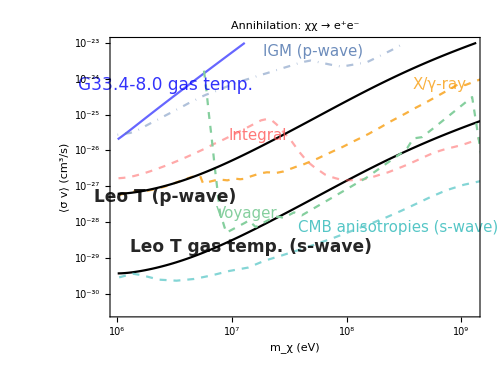

```mathematica
Show[ListLogLogPlot[{plot,plot2,data2,data3,data4,data5,data6,Transpose[{plot[[All,1]],plot[[All,2]](220/17)^2}],data7},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->500,AspectRatio->0.75,FrameTicks->{ {"",},{ticks,}},FillingStyle->{Opacity[0.3]}, PlotLabel->Style["Annihilation: χχ → e^+e^-",20,Black],FrameLabel->{Style["m_χ (eV)",20],Style["⟨σ v⟩  (cm^3/s)",20]},PlotStyle->{Black,RGBColor[0, 0, 1, 0.6],{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.72],Dashed},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],Dashed},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed},{RGBColor[0.368417, 0.506779, 0.709798, 0.49],DotDashed},Black,{RGBColor[0.772079, 0.431554, 0.102387, 0.67],Dashed}},PlotRange->{{10^6,10^9.1},{10^-23,10^-30.5}}],
Graphics[{Text[Style["Integral",RGBColor[1, Rational[1, 3], Rational[1, 3], 0.79],15],Scaled[{0.4,0.65}],{0,0},Automatic,{1,0.3}],
Text[Style["Voyager",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],15],Scaled[{0.37,0.37}],{0,0},{1,0.4}],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],17],Scaled[{0.15,0.83}],{0,0},Automatic,{1,0.75}],
Text[Style["Leo T gas temp. (s-wave)",GrayLevel[0, 0.85],Bold,17],Scaled[{0.38,0.25}],{0,0},Automatic,{1,0.4}],
Text[Style["Leo T (p-wave)",GrayLevel[0, 0.85],Bold,17],Scaled[{0.15,0.43}],{0,0},Automatic,{1,0.2}],
Text[Style["X/γ-ray",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.89,0.83}],{0,0},{1,0.47}],Text[Style["CMB anisotropies (s-wave)",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]],15],Scaled[{0.78,0.32}],{0,0},{1,0.4}],
Text[Style["IGM (p-wave)",RGBColor[0.368417, 0.506779, 0.709798, 0.91],15],Scaled[{0.55,0.95}],{0,0},{1,0.1}]}](*,ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin}}]*)]
```

### Dark neutron bounds

```mathematica
Me=0.511;
Mn=939.57;
Mp=938.27;
```

```mathematica
CMB=Import["Others/slatyer+wu2016.txt","Data"];
GammaRay=Import["Others/XGammaRay.txt","Data"];
CMBrecast=Table[{CMB[[i,1]]*1000/2+Mn,(CMB[[i,1]]*1000)/(CMB[[i,1]]*1000+2Mn)CMB[[i,2]]},{i,1,14}];
GammaRecast=Table[{GammaRay[[i,1]]/2+Mn,GammaRay[[i,1]]/(GammaRay[[i,1]]+2Mn)GammaRay[[i,2]]},{i,1,36}];
```

```mathematica
beta[Ee_]:=(1+3(-1.27)^2)/(2 Pi^3)0.97^2 (1.166 10^-5 10^-6)^2*Sqrt[Ee^2-Me^2]Ee*(Mn-Mp-Me)^2;
Γn=NIntegrate[beta[Ee],{Ee,Me,Mn-Mp}];
```

```mathematica
dnRate[m_]:=4 Pi NIntegrate[r^2 dml[r]/m (Ee-Me)/Γn beta[Ee] 4.5 10^16 ((m(1-Mn^2/m^2)/2)/10)^3 fHeat[Ee-Me],{r,0.,0.35},{Ee,Me,Mn-Mp}];
```

```mathematica
dnMWRate[m_]:= NIntegrate[rhoNFW[rc]/m (Ee-Me)/Γn beta[Ee] 4.5 10^16 ((m(1-Mn^2/m^2)/2)/10)^3 fHeat[Ee-Me],{Ee,Me,Mn-Mp}];
```

```mathematica
dnLeoT=Table[{mdn,Sqrt[coolTot/dnRate[mdn]]},{mdn,940,1050}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
dnMW=Table[{mdn,Sqrt[(nc^2 coolFunc[tc] 624)/dnMWRate[mdn]]},{mdn,940,1050}];
```

```mathematica
(*Export[dir<>"/dark neutron/dnLeoT.dat",dnLeoT,"Data"];
Export[dir<>"/dark neutron/dnMW.dat",dnMW,"Data"];
Export[dir<>"/dark neutron/dnCMB.dat",dnCMB,"Data"];
Export[dir<>"/dark neutron/dnGamma.dat",dnGamma,"Data"];*)
```

```mathematica
dnCMB=Table[{CMBrecast[[i,1]],Sqrt[1/CMBrecast[[i,2]]/(4.5 10^16((CMBrecast[[i,1]](1-Mn^2/CMBrecast[[i,1]]^2)/2)/10)^3)]},{i,1,14}];

dnGamma=Table[{GammaRecast[[i,1]],Sqrt[1/GammaRecast[[i,2]]/(4.5 10^16((GammaRecast[[i,1]](1-Mn^2/GammaRecast[[i,1]]^2)/2)/10)^3)]},{i,1,36}];
```

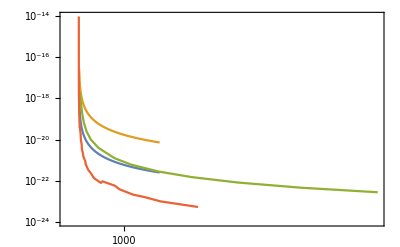

```mathematica
ListLogLogPlot[{dnLeoT,dnMW,dnCMB,dnGamma}]
```

### Extras

Please ignore this section

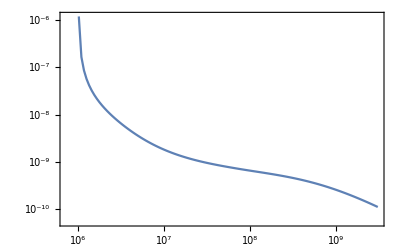

```mathematica
time=Interpolation[plot];
ListLogLogPlot[Transpose[{10^mloglist,2/time[10^mloglist] 2.5/10^(mloglist-9)19 10^6 year}],GridLines->Automatic ]
```

```mathematica
4.37 10^-27 10^3/100 19 10^6 year (1.6 10^-20 10^-6/me)  (*naive Production rate*)
```

4.60442×10^-10

```mathematica
7Sqrt[3.]/Sqrt[2] (*Turbulent velocity of Alfven modes, Subscript[u, LA]*)
```

8.57321

```mathematica
(8.57/7.74)^3 (*Mach number^3*)
```

1.35744

```mathematica
xp=0.02; 2.52 ((0.8 xp-.71 xp^2)/(0.0032+xp))0.06 (*Fer88 rescaling*)
```

0.102425

```mathematica
4/3 6.65 10^-25 cv 4 10^6 10^-12/(8 Pi) 624 (10^9 year) (*Synchrotron loss for GeV e- in GeV/Gyr*)
```

0.0833198

```mathematica
Sqrt[6 10^27 year 10^7]/kpc (*Diffusion length Ptu06 *)
```

0.44577